# Modified GUPs

A clean worksheet for Calc17.

```mathematica
(* Die neue Wahl *)
V[q_, n_] = 1/(1 + q^(n+2))

(* Die alte Wahl *)
(*V[q_, n_] = 1/(1 + q^2)*)
vSide[q_,n_, side_]:= q^(1+n) * If[side>0,V[q,n],(-1)^n V[-q,n]] 
vEff[q_,n_] = vSide[q,n,+1]HeavisideTheta[q] + vSide[q,n,-1]HeavisideTheta[-q]
vEffWirklich[q_,n_] = vSide[q,n,+1]HeavisideTheta@Re[q] + vSide[q,n,-1]HeavisideTheta@Re[-q]
```

1/(1+q^(2+n))

((-1)^n q^(1+n) HeavisideTheta[-q])/(1+(-q)^(2+n))+(q^(1+n) HeavisideTheta[q])/(1+q^(2+n))

((-1)^n q^(1+n) HeavisideTheta[-Re[q]])/(1+(-q)^(2+n))+(q^(1+n) HeavisideTheta[Re[q]])/(1+q^(2+n))

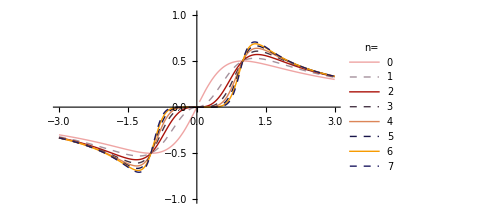

```mathematica
Plot[Table[vEff[q,n], {n,0,7}]//Evaluate,
{q,-3,3},
PlotStyle->(Riffle[#,{Dashed,#}&/@Reverse[#]]& [ColorData[9,"ColorList"]]),
PlotLegends-> LineLegend[Table[n,{n,0,7}],LegendLabel-> "n="],
PlotRange-> {-1,1},
ImageSize-> Medium]
```

## Polstellen extrahieren

Code zwar zusammenkopiert, aber drübergeschaut.

```mathematica
ReduceToSolutions[reduceResult_, extractVariable_] := Cases[reduceResult,Equal[extractVariable, value_]-> value, 100]
polReduce[n_, side_] := Reduce[Denominator@vSide[q,n, side]==0,q]
polstellenSide[n_,side_] := polReduce[n,side]~ ReduceToSolutions ~ q
polstellen[n_] := Join@@(Select[polstellenSide[n,#[[1]]], #[[2]]]&) /@ {
+1 ->  (Re[#] ≥ 0&),
-1 -> (Re[#] < 0&)
}
mitgenommenePolstellen[n_] := Select[polstellen[n], Im[#]≥ 0&]
```

```mathematica
(* Zeichne die Polstellen.
Diese Funktion/Zelle ist aus Polstellen.nb kopiert und etwas modifiziert. *)
Daten[n_] :={
{Re[#], Im[#]} & /@ (Solve[z^(2+n) == 1,z] /. {{z-> a_}-> a}) , (* in Blau *)
{Re[#], Im[#]} & /@ polstellenSide[n, +1],
{Re[#], Im[#]} & /@ polstellenSide[n, -1],
{Re[#], Im[#]} & /@ polstellen[n] (* schwarz *),
{Re[#], Im[#]} & /@ mitgenommenePolstellen[n]
}
MakePlot[n_,
label_:"Left and right hand poles"
] :=Show[ListPlot[
Daten[n],
AxesOrigin-> {0,0},
PlotRange -> {{-1.2,1.2},{-1.2,1.2}},
AspectRatio-> 1,
Frame -> True,
FrameLabel->{{Im,None},{Re,label }},
PlotMarkers -> {
{Graphics[{Lighter@Blue, Opacity[0.3],Disk[]}], 0.05},
{
Graphics@{Darker@Yellow,
Circle[],
Disk[{0,0},1,{-Pi/2,Pi/2}],
Text[Style["R","Title",15,Bold,Darker@Darker@Brown], {+0.5, Center}]},
 0.1},
{
Graphics@{Lighter@Magenta,
Circle[],
Disk[{0,0},1,{Pi/2,3/2*Pi}],
Text[Style["L","Title",15,Bold,Darker[Magenta]], {-0.5, Center}]},
 0.1},
{Graphics[{Black,Thickness[0.15],Circle[]}],0.12},
{Graphics[{Red,Thickness[0.15],Circle[]}],0.18}
},
PlotRange-> All,
ImageSize->Medium],
Graphics[{Opacity[0.2],Circle[{0,0},1]}]
];
Manipulate[Show[
MakePlot[n],
Graphics[{Text[Style[StringForm["n=``",n],{Black, 20}], Offset[{120,130},{0,0}]](*,
Text[Style[StringForm["# Residuen=``",ResidueList[n]//Length],{Black, 20}], Offset[{+30,-30},{0,0}]]*)}
]]
,{n,0,8,1}]
```

```mathematica
image=GraphicsGrid[
ArrayReshape[Join[
{ Rasterize[Show@
With[{fun = (vEffWirklich[#,0]&)},ParametricPlot[
(*just need a vis function that will allow x and y to be in the color function*)
{x,y},{x,-1.2,1.2},{y,-1.2,1.2},
(*color and mesh functions don't trigger refinement,so just use a big grid*)
PlotPoints->50,MaxRecursion->0,Mesh->50,(*turn off scaling so we can do computations with the actual complex values*)
ColorFunctionScaling->False,ColorFunction->(Hue[
(*hue according to argument,with shift so arg(z)==0 is red*)
Rescale[Arg[fun[#+I #2]],{-π,π},{0,1}+0.5],1,
(*fudge brightness a bit:
0.1 keeps things from getting too dark,
2 forces some actual bright areas*)
Rescale[Abs[fun[#+I #2]],{0,1.6},{0.21,1}]]&),
(*mesh lines according to magnitude,scaled to avoid the pole at z=1*)MeshFunctions->{Log[Abs[fun[#1+I #2]]]&},
Frame-> True,
ImageSize-> Medium,
PlotRange-> All,
FrameTicksStyle-> (FontOpacity-> 0.5),
BaseStyle->{FontSize->10} (* for export *)
]
],
 "Image", ImageResolution-> 300]
},
Table[Show[ListPlot[
Daten[n],
AxesOrigin-> {0,0},
PlotRange -> {{-1.2,1.2},{-1.2,1.2}},
AspectRatio-> 1,
Frame -> True,
FrameLabel->{{Im,None},{Re,label }},
PlotMarkers -> {
{Graphics[{Lighter@Blue, Opacity[0.3],Disk[]}], 0.05},
{
Graphics@{Darker@Yellow,
Circle[],
Disk[{0,0},1,{-Pi/2,Pi/2}],
Text[Style["R","Title",15,Bold,Darker@Darker@Brown], {+0.5, Center}]},
 0.1},
{
Graphics@{Lighter@Magenta,
Circle[],
Disk[{0,0},1,{Pi/2,3/2*Pi}],
Text[Style["L","Title",15,Bold,Darker[Magenta]], {-0.5, Center}]},
 0.1},
{Graphics[{Black,Thickness[0.15],Circle[]}],0.12},
{Graphics[{Red,Thickness[0.15],Circle[]}],0.18}
},
PlotRange-> All,
ImageSize->Medium],
Graphics[{Opacity[0.2],Circle[{0,0},1]}],
Graphics@Text[Style[StringForm["n=``",n],{Black, 20}], Offset[{130,130},{0,0}]]
],{n,0,7}]
], {3,3}]
]
```

-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
Export["../plot/modgup-poles.pdf", Show@image]
```

../plot/modgup-poles.pdf

```mathematica
Grid[Join @@ { {Style[#,{Blue, Bold, 12}]& /@
{"n", "# unique poles", "# poles","Unique Poles"}},
Table[{n,
Length@Union@polstellen[n],
Length@polstellen[n],
Union@polstellen[n] // Sort
},{n,0,7}]},
Frame -> All, Alignment-> {Left,Left}]
```

n | # unique poles | # poles | Unique Poles
0 | 2 | 2 | {-ⅈ,ⅈ}
1 | 4 | 4 | {-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3)}
2 | 4 | 4 | {-(-1)^(1/4),(-1)^(1/4),-(-1)^(3/4),(-1)^(3/4)}
3 | 4 | 4 | {-(-1)^(1/5),(-1)^(1/5),-(-1)^(4/5),(-1)^(4/5)}
4 | 6 | 6 | {-ⅈ,ⅈ,-(-1)^(1/6),(-1)^(1/6),-(-1)^(5/6),(-1)^(5/6)}
5 | 8 | 8 | {-(-1)^(1/7),(-1)^(1/7),-(-1)^(3/7),(-1)^(3/7),-(-1)^(4/7),(-1)^(4/7),-(-1)^(6/7),(-1)^(6/7)}
6 | 8 | 8 | {-(-1)^(1/8),(-1)^(1/8),-(-1)^(3/8),(-1)^(3/8),-(-1)^(5/8),(-1)^(5/8),-(-1)^(7/8),(-1)^(7/8)}
7 | 8 | 8 | {-(-1)^(1/9),(-1)^(1/9),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),-(-1)^(8/9),(-1)^(8/9)}

## Integralberechnung

```mathematica
vSide[q,n, -1]
```

((-1)^n q^(1+n))/(1+(-q)^(2+n))

```mathematica
IntegralResidueList[n_] := 
(2 Pi I) * (+1)  * Residue[vSide[q, n, Sign@Re@#] * Exp[+I q z], {q,#}]& /@ mitgenommenePolstellen[n]
IntegralValue[n_] := Total@IntegralResidueList[n]
AValue[n_] :=  2 Pi I / z * IntegralValue[n]
```

```mathematica
Grid[Join @@ { {Style[#,{Blue, Bold, 12}]& /@
{"n", "# poles","Wert für A(p)"}},
Table[{n,
Length@mitgenommenePolstellen[n],
AValue[n] // Apart
},{n,0,7}]},
Frame -> All, Alignment-> {Left,Left}]
```

n | # poles | Wert für A(p)
0 | 1 | -(2 ⅇ^-z π^2)/z
1 | 2 | -(4 ⅇ^(-(-1)^(1/6) z) π^2)/(3 z)-(4 ⅇ^((-1)^(5/6) z) π^2)/(3 z)
2 | 2 | -(ⅇ^(-(-1)^(1/4) z) π^2)/z-(ⅇ^((-1)^(3/4) z) π^2)/z
3 | 2 | -(4 ⅇ^(-(-1)^(3/10) z) π^2)/(5 z)-(4 ⅇ^((-1)^(7/10) z) π^2)/(5 z)
4 | 3 | -(2 ⅇ^((-1)^(2/3) z) π^2)/(3 z)-(2 ⅇ^(-z-(-1)^(1/3) z) (ⅇ^z+ⅇ^((-1)^(1/3) z)) π^2)/(3 z)
5 | 4 | -(4 ⅇ^((-1)^(13/14) z) π^2)/(7 z)-1/(7 z)4 ⅇ^(-(-1)^(1/14) z-(-1)^(5/14) z) (ⅇ^((-1)^(1/14) z)+ⅇ^((-1)^(5/14) z)+ⅇ^((-1)^(1/14) z+(-1)^(5/14) z+(-1)^(9/14) z)) π^2
6 | 4 | -(ⅇ^((-1)^(7/8) z) π^2)/(2 z)-(ⅇ^(-(-1)^(1/8) z-(-1)^(3/8) z) (ⅇ^((-1)^(1/8) z)+ⅇ^((-1)^(3/8) z)+ⅇ^((-1)^(1/8) z+(-1)^(3/8) z+(-1)^(5/8) z)) π^2)/(2 z)
7 | 4 | -(4 ⅇ^((-1)^(5/6) z) π^2)/(9 z)-1/(9 z)4 ⅇ^(-(-1)^(1/6) z-(-1)^(7/18) z) (ⅇ^((-1)^(1/6) z)+ⅇ^((-1)^(7/18) z)+ⅇ^((-1)^(1/6) z+(-1)^(7/18) z+(-1)^(11/18) z)) π^2